This file accompanies exercise from Chapter 12: Parameter Estimation, Sloppiness, and Model Identifiability – D Daniels, M Dobrzyński, D. Fey of the book Quantitative Biology: Theory, Computational Methods and Examples of Models

Last modification 27.11.2017

## Definitions

### general

```mathematica
mmfunc[s_,v_,k_]:=v(s/k)/(1+s/k)(* Michaelis-Menten kinetics with Vmax=v, Km=k (halfamx) *)
```

### kinetic parameters

```mathematica
kinpars={
v1->0.5,v2->5,
v3->5,v4->0.03,
v5->0.1,v6->0.1,
k1->0.1,k2->0.1,
k3->0.1,k4->0.1,
k5->1,k6->10};
```

### kinetic equations

Parameters α and β control whether the unknown phosphatase X transmits feedback to g1 and/or g2: 
α=1, β=0	active X (Xact) catalyzes g1p dephoshorylation only (link number 1 in Fig. 12.7)
α=1, β=1	Xact catalyzes g1p AND g2p dephoshorylation (links 1 & 2 in Fig. 12.7)
α=0, β=1	Xact catalyzes g2p dephoshorylation only (link 2 in Fig. 12.7)
α=0, β=0	Xact doesn’t affect upstream components

gIN	input stimulation

```mathematica
vars={g1p[t],g2p[t],Xact[t]};
syst={
g1p'[t]==V1-V2,
g2p'[t]==V3-V4,
Xact'[t]==V5-V6
};
vsubst={
V1->gIN  w1,V2-> w2 (1+α(a62-1)), 
V3-> g1p[t] w3, V4-> w4 (1+β(a64-1)),
V5-> g2p[t] w5, V6-> w6};
wsubst={
w1-> mmfunc[g1[t],v1,k1],w2->mmfunc[g1p[t],v2,k2],
w3-> mmfunc[g2[t],v3,k3],w4->mmfunc[g2p[t],v4,k4],
w5-> mmfunc[Xinact[t],v5,k5],w6->mmfunc[Xact[t],v6,k6]};
asubst={a62->Xact[t], a64->Xact[t]};
conserv={
g1[t]->g1tot-g1p[t],
g2[t]->g2tot-g2p[t],
Xinact[t]->Xtot-Xact[t]};
systsubst=syst/.vsubst/.wsubst/.asubst/.conserv;
```

## System 1-3: 2-step cascade with negative feedback through intermediate component X to g1 and/or g2 dephosphorylation

#### testing parameters

Checkbox MANalpha and MANbeta allow to switch between different feedback modes as described above.

```mathematica
Manipulate[Plot[
Evaluate[
g2p[t]/.NDSolve[{systsubst/.{
v1->MANpv1,v2->MANpv2,
v3->MANpv3,v4->MANpv4,
v5->MANpv5,v6->MANpv6,
k1->MANpk1,k2->MANpk2,
k3->MANpk3,k4->MANpk4,
k5->MANpk5,k6->MANpk6,
gIN->MANinput,
g1tot->MANg1tot,
g2tot->MANg2tot,
Xtot ->MANXtot,
α->MANalpha,
β->MANbeta},
g1p[0]==0,
g2p[0]==0,
Xact[0]==0},
{g1p,g2p,Xact},{t,0,1000}]], 
{t,0,1000},
PlotRange->{{0,100}, {0,1}}], 
{{MANpv1, .5}, 0, 10},{{MANpv2, 5}, 0, 10},
{{MANpv3, 5}, 0, 10},{{MANpv4, .03}, 0, 10},
{{MANpv5, .1}, 0, 10},{{MANpv6, .1}, 0, 10},
{{MANpk1, .1}, 0, 10},{{MANpk2, .1}, 0, 10},
{{MANpk3, .1}, 0, 10},{{MANpk4, .1}, 0, 10},
{{MANpk5, 1}, 0, 10},{{MANpk6, 10}, 0, 100},
{{MANinput, .1}, 0, 10},
{{MANg1tot, 1}, 0, 2},
{{MANg2tot, 1}, 0, 2},
{{MANXtot, 1}, 0, 2},
{{MANalpha, 1}, {0, 1}},
{{MANbeta, 0}, {0,1}}]
```

## Model comparison

### F-n

This function returns a timecourse for g2p dependning on the following input parameters:
INinput - input concentrations
INXtot - total concentration of the feedback component X
INalpha - switch for coupling Xact to g1p dephosphorylation (0 - off, 1 - on)
INbeta - switch for coupling Xact to g2p dephosphorylation (0 - off, 1 - on)

```mathematica
g2pOFpars[INinput_,INg3tot_, INalpha_, INbeta_ ]:=g2p[t]/.NDSolve[{systsubst/.kinpars/.{
gIN->INinput,
Xtot ->INg3tot,
α->INalpha,
β->INbeta}/.{g1tot->1,g2tot->1},
g1p[0]==0,
g2p[0]==0,
Xact[0]==0},
{g1p,g2p,Xact},{t,0,1000}]
```

### Plots

```mathematica
tabLineStyle={Thick,Dashed,Dotted,DotDashed};
tPts = {0,5,10,30,60};
inConc={0.01,0.02,0.1};
```

#### Create a table with g2p responses at discrete time points (to mimic experimental results) for a range of input stimuli

```mathematica
Table[
Table[{xx, Evaluate[g2pOFpars[inConc[[ii]],0.05,1,0]][[1]]/.t->xx}, {xx, tPts}],
{ii,1,3,1}]
```

{{{0,0.},{5,0.199223},{10,0.581724},{30,0.502132},{60,0.163754}},{{0,0.},{5,0.411961},{10,0.928809},{30,0.763125},{60,0.514924}},{{0,0.},{5,0.996679},{10,0.99501},{30,0.974968},{60,0.972314}}}

#### Plot time courses at discrete time points (to mimic experimental results) for a range of input stimuli

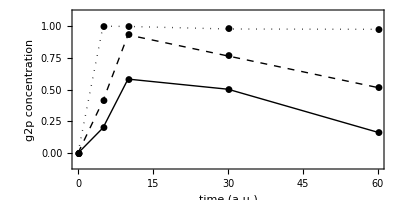

```mathematica
Show[
Table[
ListPlot[Table[{xx, Evaluate[g2pOFpars[inConc[[ii]],0.05,1,0]][[1]]/.t->xx}, {xx, tPts}], 
Joined->True,
PlotMarkers->Automatic,
PlotRange->{All,{-0.1,1.1}},
Frame->True,
FrameLabel->{"time (a.u.)","g2p concentration"},
Ticks->True,
BaseStyle->{FontSize->16,FontFamily->"Helvetica",FontWeight->"Bold"}, 
PlotStyle->{Thick,Black,tabLineStyle[[ii]]},
AspectRatio->0.5,
ImageSize->400],
{ii,1,3,1}]
]
```

#### Plot simulated time courses for 4 combinations of the negative feedback from X

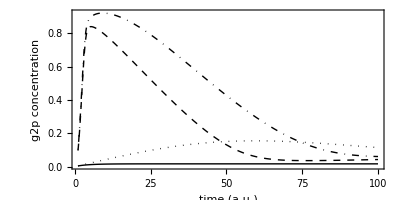

```mathematica
Show[
Table[Plot[Evaluate[g2pOFpars[0.1,1,xx,yy]],
{t,1,100},
PlotRange->All,
Frame->True,
FrameLabel->{"time (a.u.)","g2p concentration"},
Ticks->True,
BaseStyle->{FontSize->16,FontFamily->"Helvetica",FontWeight->"Bold"}, 
PlotStyle->{Thick,Black,tabLineStyle[[1+xx 2^0+yy 2^1]]},
AspectRatio->0.5,
ImageSize->400],
 {yy, 0, 1, 1},{xx, 0 , 1, 1}]
]
```